```mathematica
(*Capacitante function parameters*)
SetDirectory[NotebookDirectory[]];
τ2=0.5;τ4=1;C0=1;
case=3;point=4;
Switch[case,
1,T=100;prefix="Fig4a_";,
2,T=30;prefix="Fig4b_";,
3,T=6;prefix="Fig4c_"
];

Switch[point,
(*1,δ=0.05;C1=0.7;filename=prefix<>"example1.png";,*)
1,δ=0.17;C1=0.7;filename=prefix<>"example1.png";,
2,δ=0.25;C1=0.7;filename=prefix<>"example2.png";,
3,δ=0.17;C1=0.3;filename=prefix<>"example3.png";,
4,δ=0.25;C1=0.3;filename=prefix<>"example4.png"
];
τ1=0.2+δ;τ3=0.7+δ;
(*FHN Parameters*)
ep=0.08;β=0.65;γ=0.7;maxtime=300;
Ct[t_]=Which[Mod[t,T]<τ1 T,C0,Mod[t,T]<τ2 T,C0+(Mod[t,T]-τ1 T)(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,C1, True,C1+(Mod[t,T]-τ3 T)(C0-C1)/(T- τ3 T)];
(*Ctd[t_]=Which[Mod[t,T]<τ1 T,0,Mod[t,T]<τ2 T,(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,0, True,(C0-C1)/(T- τ3 T)];*)
(*Look for stable equilibrium*)
eqn=FindRoot[0==v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;
```

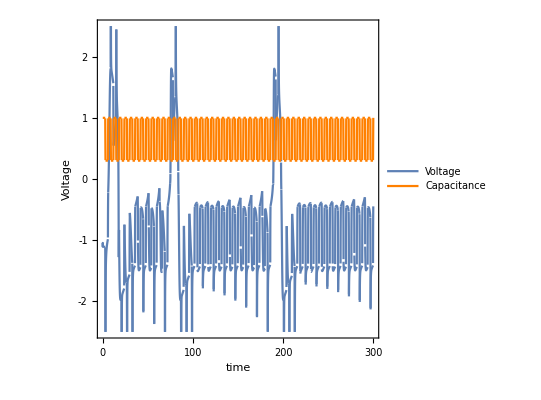

Fig4c_example4.png

```mathematica
(*{V,W}=NDSolveValue[{Ct[t] v'[t]+v[t] Ctd[t] ==v[t]-v[t]^3/3-w[t],w'[t]==ep(v[t]-γ w[t] + β),v[0]==v0,w[0]==w0},{v,w},{t,0,maxtime},MaxStepSize->0.2Min[τ2-τ1,1-τ3]T];*)
{U,W}=NDSolveValue[{u'[t] ==u[t]/Ct[t]-u[t]^3/(3Ct[t]^3)-w[t],w'[t]==ep(u[t]/Ct[t]-γ w[t] + β),u[0]==Ct[0]v0,w[0]==w0},{u,w},{t,0,maxtime},MaxStepSize->0.2Min[τ2-τ1,1-τ3]T];
(*Voltage/capacitance plot*)
voltage=Plot[U[t]/Ct[t],{t,0,maxtime},
(*voltage=Plot[V[t],{t,0,maxtime},*)
PlotRange->{-2.5,2.5},
TicksStyle->Directive[FontSize->16],
Frame->True,
FrameLabel->{{"Voltage","Capacitance"},{"time",None}},
LabelStyle->Directive[Black,FontSize->16],
FrameTicks->{{All,All},{All,None}},
PlotPoints->10000,
MaxRecursion->3
];
capacitance=Plot[{Ct[t]},{t,0,maxtime},
PlotPoints->10000,
MaxRecursion->3,
PlotStyle->Orange
];

g1=Legended[Show[voltage, capacitance,AspectRatio->1],Placed[LineLegend[{ColorData[97,"ColorList"][[1]],Orange},{Style["Voltage",FontSize->18],Style["Capacitance",FontSize->18]},LegendLayout->"Row"],{{0.5,0.93}}]]
Export[filename,g1]
```